```mathematica
y1=0;
y2=1;
```

```mathematica
x1=0;
x2=T;
```

```mathematica
k1=0;
k2=0;
```

```mathematica
t[x_]:=(x-x1)/(x2-x1)
```

```mathematica
a=k1(x2-x1)-(y2-y1);
b=-k2(x2-x1)+(y2-y1);
```

```mathematica
q[x_]=(1-t[x])y1+t[x] y2+t[x](1-t[x])((1-t[x])a+b t[x])//Simplify
```

((3 T-2 x) x^2)/T^3

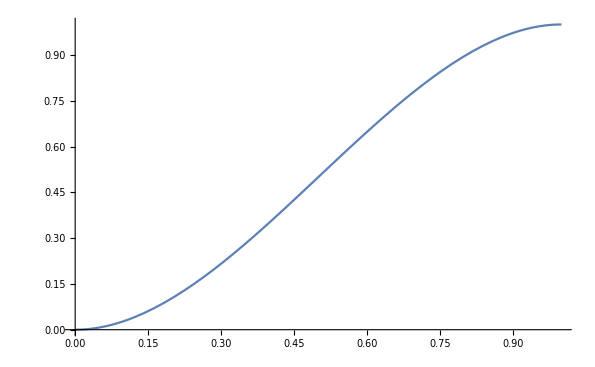

```mathematica
Plot[q[x]/.T->1,{x,0,1}]
```